```mathematica
numb1={52};
numb2={52};
latvec1={100,100};
latvec2={100,100,100};
sigma={3.401};
epsilon={0.978638};
rad=2.5;
b=8.314462618*^-3*87.3;
cutoff=10;
config1=Table[RandomReal[],#,3]&/@numb1*latvec1[[1]]-latvec1[[1]]/2;

config2=Table[RandomReal[],#,3]&/@numb2*latvec2[[1]]-latvec2[[1]]/2;

configEpbc[config_,cutoff_,latvec_,epsilon_,sigma_]:=Module[{dist,utot},dist=Flatten[Table[If[i==j&&k==l &&a==b==c==0,Nothing,{i,j,EuclideanDistance[config[[i,k]],config[[j,l]]+{a,b,c}*latvec]}],{i,Length[config]},{j,Length[config]},{k,Length[config[[i]]]},{l,Length[config[[j]]]},{a,-1,1},{b,-1,1},{c,-1,1}],6];
utot=Sum[If[i[[3]]>cutoff,0,4*((epsilon[[i[[1]]]]+epsilon[[i[[2]]]])^0.5)*(((sigma[[i[[1]]]]+sigma[[i[[2]]]])/(i[[3]]))^12-((sigma[[i[[1]]]]+sigma[[i[[2]]]])/(i[[3]]))^6)],{i,dist}];
N[utot/2]];

randmove[stepleng_]:=Module[{localConfig={config1,config2},cho0,cho,cho1,cho2,oldE,temp,newE,lat={latvec1,latvec2}},
cho0=RandomInteger[{1,2}];
cho=RandomInteger[{1,Length[localConfig[[cho0]]]}];
cho1=RandomInteger[{1,Length[localConfig[[cho0]][[cho]]]}];
cho2=Table[RandomReal[{-1,1}]*stepleng/100,3]*lat[[cho0]];
oldE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
localConfig[[cho0]][[cho]][[cho1]]=localConfig[[cho0]][[cho]][[cho1]]+cho2;

temp=MapThread[#1>#2&,{lat[[cho0]],localConfig[[cho0]][[cho]][[cho1]]}];
localConfig[[cho0]][[cho]][[cho1]]=MapThread[If[#1,#2,#2-#3]&,{temp,localConfig[[cho0]][[cho]][[cho1]],lat[[cho0]]}];
newE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
If[RandomReal[]<N[Exp[-(1/b)*(newE-oldE)]],localConfig,{config1,config2}]
];

volchange[length_]:=Module[{cho,oldE,lat1=latvec1,lat2=latvec2,con1=config1,con2=config2,newE},
cho=RandomReal[{-1,1}]*length;
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con1=con1*(lat1[[1]]-cho)/lat1[[1]];
con2=con2*(lat2[[1]]+cho)/lat2[[1]];
lat1=lat1+cho;
lat2=lat2-cho;
newE=configEpbc[con1,cutoff,lat1,epsilon,sigma]+configEpbc[con2,cutoff,lat2,epsilon,sigma];
If[RandomReal[]<N[N[Exp[-(1/b)*(newE-oldE)]]*((lat1[[1]]^(3*Total[numb1]))*(lat2[[1]]^(3*Total[numb2])))/((latvec1[[1]]^(3*Total[numb1]))*(latvec2[[1]]^(3*Total[numb2])))],{con1,con2,lat1,lat2},{config1,config2,latvec1,latvec2}]
];

den:=(
{numb1[[1]]/latvec1[[1]]^3,numb2[[1]]/latvec2[[1]]^3})
paraexchange[]:=Module[{num,con,cho,cho1,cho2,oldE,lat,newE},
num={numb1,numb2};
con={config1,config2};
lat={latvec1,latvec2};
cho=RandomInteger[{1,2}];
cho1=RandomInteger[{1,Length[con[[cho]]]}];
cho2=RandomInteger[{1,Length[con[[cho]][[cho1]]]}];
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con[[3-cho]][[cho1]]=Append[con[[3-cho]][[cho1]],Table[RandomReal[{-1,1}],3]*lat[[3-cho]]];
con[[cho]][[cho1]]=Delete[con[[cho]][[cho1]],cho2];
newE=configEpbc[con[[1]],cutoff,lat[[1]],epsilon,sigma]+configEpbc[con[[2]],cutoff,lat[[2]],epsilon,sigma];
num[[cho]][[cho1]]=num[[cho]][[cho1]]-1;
num[[3-cho]][[cho1]]=num[[3-cho]][[cho1]]+1;
If[RandomReal[]<N[N[Exp[-(1/b)*(newE-oldE)]]*((Total[num[[cho]]]+1)*lat[[3-cho]][[1]]^3)/(Total[num[[3-cho]]]*lat[[cho]][[1]]^3)],{con[[1]],con[[2]],num[[1]],num[[2]]},{config1,config2,numb1,numb2}]
];
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
conE={}
densi={}
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[];conE=Append[conE,configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]];densi=Append[densi,den],100];
Length[config1[[1]]]
Length[config2[[1]]]
numb1
numb2
latvec1
latvec2
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
```

1364.53

{}

{}

General::munfl: Exp[-116208.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7672.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23491.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

35

69

{35}

{69}

{85.1197,85.1197,85.1197}

{114.88,114.88,114.88}

-23.8048

3.67988

```mathematica
ListPointPlot3D[config2[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]]}]
ListPointPlot3D[config1[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]]}]
```

Automatic::prng: Value of option PlotRange -> {-114.88,114.88,-114.88,114.88,-114.88,114.88} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

Automatic::prng: Value of option PlotRange -> {-85.1197,85.1197,-85.1197,85.1197,-85.1197,85.1197} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

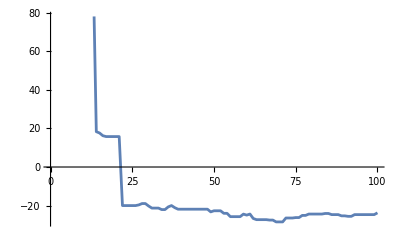

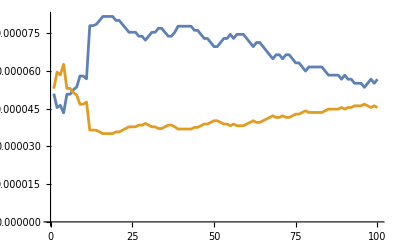

```mathematica
ListLinePlot[conE]
ListLinePlot[{Transpose[densi][[1]],Transpose[densi][[2]]}]
```

```mathematica
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[],50];
```

{100,100,100}

-Graphics3D-

1

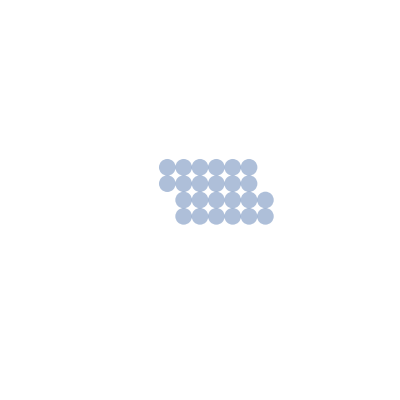

```mathematica
point={{0,0},{1,0},{0,-1},{-1,0},{1,-1},{-1,-1}};
latve={{3,0},{0,3}};
addp=point+Table[{3,0},Length[point]];
Table[point=Append[point,i],{i,addp}];
addp=point+Table[{-1,2},Length[point]];
Table[point=Append[point,i],{i,addp}];

ListPlot[point,PlotStyle->Directive[PointSize[0.03],Opacity[0.5]],Axes->False,PlotRange->{{-10,10},{-10,10}},AspectRatio->1]
```

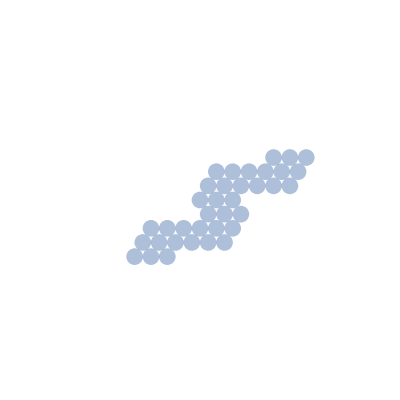

```mathematica
point2={{0,0},{1,0},{2,0},{0.5,0.5*3^0.5},{1.5,0.5*3^0.5},{2.5,0.5*3^0.5},{1,3^0.5},{2,3^0.5},{3,3^0.5}};
addp=point2+Table[{3,0}-1*{-1.5,-1.5*3^0.5}/3,Length[point2]];
Table[point2=Append[point2,i],{i,addp}];
addp=point2+Table[{-1.5,-1.5*3^0.5}*4/3-{3,0}*2/3,Length[point2]];
Table[point2=Append[point2,i],{i,addp}];

ListPlot[point2,PlotStyle->Directive[PointSize[0.03],Opacity[0.5]],Axes->False,PlotRange->{{-10,10},{-10,10}},AspectRatio->1]
```

```mathematica
point3=Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2];
lat={{2,0,0},{0,2,0},{0,0,2}}
addp=point3+Table[lat[[1]]-lat[[2]]*0/2,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[2]]-lat[[3]]*1/2,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[3]]-lat[[1]]*1/2,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
Length[Counts[point3]]
Length[point3]
ListPointPlot3D[point3,BoxRatios->{1,1,1},PlotRange->{{-5,5},{-5,5},{-5,5}},PlotStyle->Directive[PointSize[0.03],Opacity[0.5]]]
```

{{2,0,0},{0,2,0},{0,0,2}}

64

64

-Graphics3D-

```mathematica
point3=Flatten[Table[{i,j,k},{i,-1,1},{j,-1,1},{k,-1,1}],2];
lat={{3,0,0},{0,3,0},{0,0,3}}
addp=point3+Table[lat[[1]]-lat[[2]]*3/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[2]]-lat[[3]]*2/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[3]]-lat[[1]]*1/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
Length[Counts[point3]]
Length[point3]
ListPointPlot3D[point3,BoxRatios->{1,1,1},PlotRange->{{-5,5},{-5,5},{-5,5}},PlotStyle->Directive[PointSize[0.03],Opacity[0.8]]]
```

{{3,0,0},{0,3,0},{0,0,3}}

210

216

```mathematica
point3=Flatten[Table[{i,j,k},{i,-1,1},{j,-1,1},{k,-1,1}],2];
lat={{3,0,0},{0,3,0},{0,0,3}};
addp=point3+Table[lat[[1]]*4/3-lat[[2]]*0/3-lat[[3]]*0/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[2]]-lat[[3]]*2/3-lat[[1]]*0/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[3]]-lat[[1]]*2/3-lat[[2]]*0/3,Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
counts=Counts[point3];
uniquePoints=Select[point3,counts[#]==1&];
repeatedPoints=Select[point3,counts[#]>1&];
plotUnique=ListPointPlot3D[uniquePoints,PlotStyle->Directive[PointSize[0.03],Opacity[0.5]],BoxRatios->{1,1,1},PlotRange->{{-5,5},{-5,5},{-5,5}}];
plotRepeated=ListPointPlot3D[repeatedPoints,PlotStyle->Directive[PointSize[0.03],Red],BoxRatios->{1,1,1},PlotRange->{{-5,5},{-5,5},{-5,5}}];
Show[plotUnique,plotRepeated]
```

-Graphics3D-

```mathematica
point3=Flatten[Table[{i,j,k},{i,-5,5},{j,-5,5},{k,-5,5}],2];
Length[point3]

lat={{11,0,0},{0,11,0},{0,0,11}};
lat={lat[[1]]-lat[[2]]*3/11,lat[[2]]-lat[[3]]*1/11,lat[[3]]-lat[[1]]*1/11};
addp=point3+Table[lat[[1]],Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[2]],Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
addp=point3+Table[lat[[3]],Length[point3]];
Table[point3=Append[point3,i],{i,addp}];
counts=Counts[point3];
uniquePoints=Select[point3,counts[#]==1&];
repeatedPoints=Select[point3,counts[#]>1&]
plotUnique=ListPointPlot3D[uniquePoints,PlotStyle->Directive[PointSize[0.03],Opacity[0.3]],BoxRatios->{1,1,1}];
plotRepeated=ListPointPlot3D[repeatedPoints,PlotStyle->Directive[PointSize[0.03],Red],BoxRatios->{1,1,1}];
Show[plotUnique,plotRepeated]
```

1331

{{5,3,5},{5,4,5},{5,5,5},{5,3,5},{5,4,5},{5,5,5}}

-Graphics3D-

```mathematica
num1=250;
num2=250;
numb={250,250};

MinimizeDifference[n_Integer]:=Module[{factors,bestTriple={1,1,n},minDiff=n-1},factors=Select[Divisors[n],#<=n/4&];
Do[Do[If[i*j<=n&&IntegerQ[n/(i*j)],k=n/(i*j);
If[Max[i,j,k]-Min[i,j,k]<minDiff,minDiff=Max[i,j,k]-Min[i,j,k];
bestTriple={i,j,k};]],{j,factors}],{i,factors}];
bestTriple];

findlatbcc[num_,spac_]:=Module[{try,lat,lat2,vec},
try=num+1;
While[Min[MinimizeDifference[try]]<3,try=try+1];
vec=MinimizeDifference[try];
lat={{vec[[3]],0,0},{0,vec[[2]],0},{0,0,vec[[1]]}};
lat2={lat[[1]]-(try-num)*lat[[2]]/vec[[2]],lat[[2]]-lat[[3]]/vec[[3]],lat[[3]]-lat[[1]]/vec[[1]]};
{lat*spac,lat2*spac,vec}
];

initbcc[tr_,spac_,numb_]:=Module[{bcc},
bcc=Flatten[Table[{i,j,k},{i,0,spac*(tr[[3]]-1),spac},{j,0,spac*(tr[[2]]-1),spac},{k,0,spac*(tr[[1]]-1),spac}],2];
Do[bcc=DeleteCases[bcc,{spac*(tr[[3]]-1),j,spac*(tr[[1]]-1)}],{j,spac*(tr[[2]]-(tr[[1]]*tr[[2]]*tr[[3]])+numb),spac*(tr[[2]]-1),spac}];
{bcc+Table[Table[RandomVariate[NormalDistribution[0,spac/10]],3],Length[bcc]],{spac*(tr[[3]]-1),(tr[[2]]-(tr[[1]]*tr[[2]]*tr[[3]])+numb)*spac,spac*(tr[[1]]-1)},{spac*(tr[[3]]-1),(tr[[2]]-(tr[[1]]*tr[[2]]*tr[[3]])+numb-1)*spac,spac*(tr[[1]]-1)}}
];

findec[lat_,config_,tr_]:=Module[{spc},
spc=lat[[1]][[1]]/tr[[3]];

Flatten[Table[{{i,i+spc},{j,j+spc},{j,j+spc}},{i,0,spc*(tr[[3]]-1),spc},{j,0,spc*(tr[[2]]-1),spc},{k,0,spc*(tr[[1]]-1),spc}],2]];


rearr[config_,tr_]:=Module[{},
aaa
];
sys={{config,lat1,lat2,spac,try},{}};

exchaparti[]:=Module[{num=numb,sy=sys},
cho=RandomInteger[{1,2}];
num[[cho]]=num[[cho]]-1;
num[[3-cho]]=num[[3-cho]]+1;
sy1[[cho]];
];



sys1={initbcc[MinimizeDifference[findlatbcc[num1][[3]]],4,num1][[1]],initbcc[MinimizeDifference[findlatbcc[num1][[3]]],4,num1][[2]],initbcc[MinimizeDifference[findlatbcc[num1][[3]]],4,num1][[3]],findlatbcc[num1,4][[1]],findlatbcc[num1,4][[2]],4,findlatbcc[num1,4][[3]]};
Nearest[sys1[[1]],sys1[[3]]]
pos=Sphere[#,1]&/@sys1[[1]];
Graphics3D[pos,Axes->True,AxesLabel->{"X","Y","Z"}]
findec[,initbcc[MinimizeDifference[findlatbcc[num1][[3]]],4,num1][[1]],findlatbcc[num1][[4]]];
```

{{24.3046,12.2845,20.136}}

-Graphics3D-

Part::partw: Part 4 of {{{7,0,0},{0,6,0},{0,0,6}},{{7,-2,0},{0,6,-6/7},{-7/6,0,6}},252} does not exist.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of {{{7,0,0},{0,6,0},{0,0,6}},{{7,-2,0},{0,6,-6/7},{-7/6,0,6}},252}⟦4⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {i,0,(Null (-1+{{{«3»},{«3»},{«3»}},{{«3»},{«3»},{«3»}},252}⟦4⟧⟦3⟧))/({{{«3»},{«3»},{«3»}},{{«3»},{«3»},{«3»}},252}⟦4⟧⟦3⟧),Null/({{{«3»},{«3»},{«3»}},{{«3»},{«3»},{«3»}},252}⟦4⟧⟦3⟧)} does not have appropriate bounds.

-Graphics3D-

```mathematica
a={{1,2,3},{2,3,4}}
a*2
```

{{1,2,3},{2,3,4}}

{{2,4,6},{4,6,8}}